```mathematica
Clear["Global`*"];
```

## 问题 1

## 第 1 小问

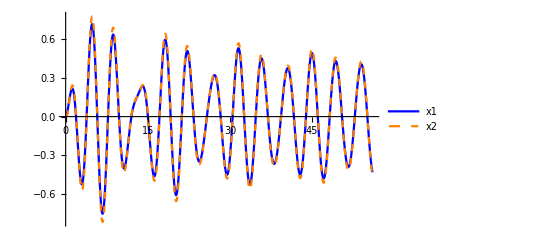

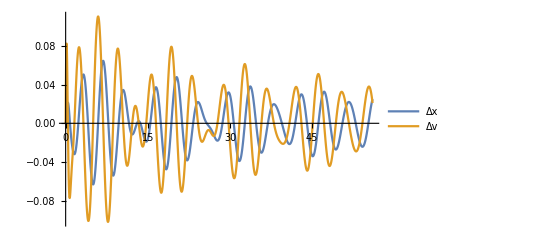

```mathematica
m=2433;k=80000;c=10000;
f=6250;omega=1.4005;k1=1025*9.8*Pi;
c0=656.3616;m0=1335.535;M=4866;
stop=40*omega;
s=NDSolve[{m*x2''[t]==k(x1[t]-x2[t])+c(x1'[t]-x2'[t]),f*Cos[omega*t]==k(x1[t]-x2[t])+c(x1'[t]-x2'[t])+k1*x1[t]+c0*x1'[t]+m0*x1''[t]+M*x1''[t],x1[0]==x2[0]==x1'[0]==x2'[0]==0},{x1,x2},{t,0,Max[stop,100]}];
Plot[Evaluate[{x1[t],x2[t]}/.s],{t,0,stop},PlotLegends->{"x1","x2"},PlotStyle->{Directive[Blue,Thick],Directive[Orange,Dashed]}]
Plot[Evaluate[{x1[t]-x2[t],x1'[t]-x2'[t]}/.s],{t,0,stop},PlotLegends->{"Δx","Δv"}]
```

```mathematica
targets={10,20,40,60,100};
data=Table[{i,First[x1[i]/.s],First[x1'[i]/.s],First[x2[i]/.s],First[x2'[i]/.s]},{i,targets}];
Grid[data,Frame->All]
Export["~/cumcm/cumcm-code/P11-paper.xlsx",data]
```

10 | -0.190711 | -0.641009 | -0.211679 | -0.693954
20 | -0.590684 | -0.240952 | -0.634248 | -0.272776
40 | 0.285375 | 0.312971 | 0.296499 | 0.332912
60 | -0.314505 | -0.479456 | -0.331435 | -0.515729
100 | -0.083614 | -0.604211 | -0.0840672 | -0.643002

~/cumcm/cumcm-code/P11-paper.xlsx

```mathematica
Twave=1/omega
Ttargets=Table[i,{i,Range[0,40,Twave]}];
Export["~/cumcm/cumcm-code/P11.xlsx",Flatten[Table[{i,x1[i],x1'[i],x2[i],x2'[i]}/.s,{i,Ttargets}],1]]
```

0.714031

~/cumcm/cumcm-code/P11.xlsx

## 第 (2) 小问

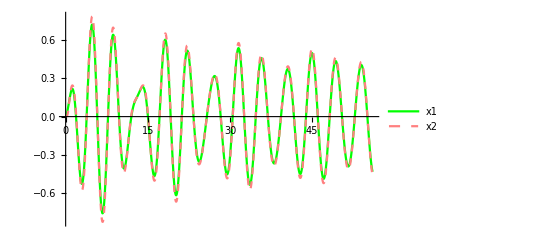

~/cumcm/cumcm-code/P12-paper.xlsx

10 | -0.191991 | -0.644618 | -0.213781 | -0.701741
20 | -0.59419 | -0.245594 | -0.640176 | -0.28171
40 | 0.282215 | 0.306276 | 0.294026 | 0.325993
60 | -0.317233 | -0.482805 | -0.335615 | -0.520822
100 | -0.0848249 | -0.605817 | -0.0862467 | -0.645578

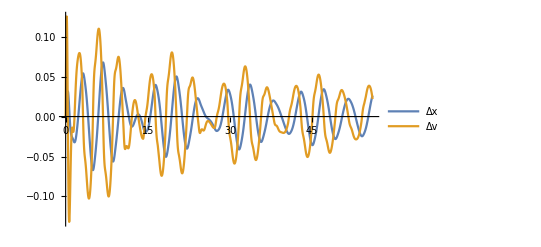

~/cumcm/cumcm-code/P12.xlsx

```mathematica
cv2[v_]:=10000*Sqrt[Abs[v]]
s=NDSolve[{m*x2''[t]==k(x1[t]-x2[t])+cv2[x2'[t]]*(x1'[t]-x2'[t]),f*Cos[omega*t]==k(x1[t]-x2[t])+cv2[x2'[t]]*(x1'[t]-x2'[t])+k1*x1[t]+c0*x1'[t]+m0*x1''[t]+M*x1''[t],x1[0]==x2[0]==x1'[0]==x2'[0]==0},{x1,x2},{t,0,Max[stop,100]}];
Plot[Evaluate[{x1[t],x2[t]}/.s],{t,0,stop},PlotLegends->{"x1","x2"},PlotStyle->{Directive[Green,Thick],Directive[Pink,Dashed]}]
Export["~/cumcm/cumcm-code/P12-paper.xlsx",Flatten[Table[{i,x1[i],x1'[i],x2[i],x2'[i]}/.s,{i,targets}]]]
Grid[Flatten[Table[{i,x1[i],x1'[i],x2[i],x2'[i]}/.s,{i,targets}],1],Frame->All]
Plot[Evaluate[{x1[t]-x2[t],x1'[t]-x2'[t]}/.s],{t,0,stop},PlotLegends->{"Δx","Δv"}]
Export["~/cumcm/cumcm-code/P12.xlsx",Flatten[Table[{i,x1[i],x1'[i],x2[i],x2'[i]}/.s,{i,Ttargets}],1]]
```

```mathematica
M=4866;m=2433;k=80000;c=10000;omega=2.2143;k1=1025*9.8*Pi;
f=4890;c0=167.8395;m0=1165.992;
```

```mathematica
start=510;stop=520;dim=0.01;
P2[cm2_]:=Sum[cm2*((x1'[i]-x2'[i])^2)*dim,{i,start,stop,dim}]/.NDSolve[{m*x2''[t]==k*(x1[t]-x2[t])+cm2*(x1'[t]-x2'[t]),f*Cos[omega*t]==k*(x1[t]-x2[t])+cm2*(x1'[t]-x2'[t])+k1*x1[t]+c0*x1'[t]+m0*x1''[t]+M*x1''[t],x1[0]==x2[0]==x1'[0]==x2'[0]==0},{x1,x2},{t,start,stop}]
```

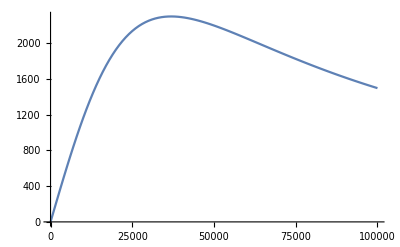

```mathematica
DrawP2[pStart_,pStop_,pStepNum_]:=ListLinePlot[Table[{i,First[P2[i]]},{i,Range[pStart,pStop,(pStop-pStart)/pStepNum]}]]
DrawP2[0,100000,100]
```

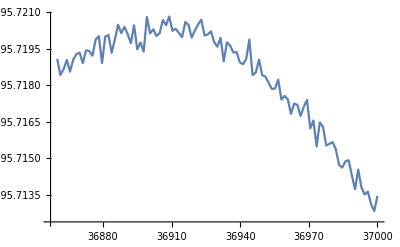

```mathematica
DrawP2[36860,37000,100]
```

```mathematica
start=510;stop=520;dim=0.01;
M=4866;m=2433;k=80000;c=10000;omega=2.2143;k1=1025*9.8*Pi;
f=4890;c0=167.8395;m0=1165.992;
cmv2[v_,ck_,ce_]:=ck*Abs[v]^ce;
P22I[ck_,ce_]:=NDSolve[{m*x2''[t]==k*(x1[t]-x2[t])+cmv2[x1'[t]-x2'[t],ck,ce]*(x1'[t]-x2'[t]),f*Cos[omega*t]==k*(x1[t]-x2[t])+cmv2[x1'[t]-x2'[t],ck,ce]*(x1'[t]-x2'[t])+k1*x1[t]+c0*x1'[t]+m0*x1''[t]+M*x1''[t],x1[0]==x2[0]==x1'[0]==x2'[0]==0},{x1,x2},{t,start,stop}]
P22[ck_,ce_]:=Sum[cmv2[x1'[i]-x2'[i],ck,ce+2]*dim,{i,start,stop,dim}]/.P22I[ck,ce]
```

```mathematica
CalcP22[kStart_,kStop_,kStepNum_,eStart_,eStop_,eStepNum_]:=Parallelize[Table[{pe,ppk,First[P22[ppk,pe]]},{ppk,Range[kStart,kStop,(kStop-kStart)/kStepNum]},{pe,Range[eStart,eStop,(eStop-eStart)/eStepNum]}]]
DrawP22[data_]:=ListPlot3D[Flatten[data,1]]
s=CalcP22[0,100000,8,0,1,8];
```

-Graphics3D-

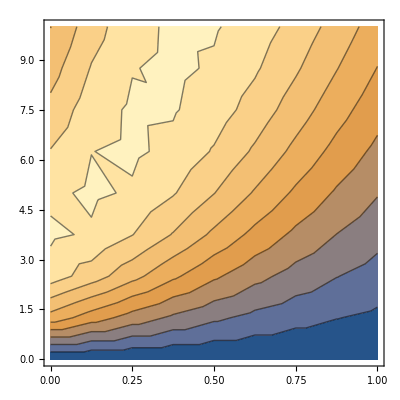

```mathematica
ss=Table[{i[[1]],i[[2]]/10000,i[[3]]},{i,Flatten[s,1]}];
(*Grid[N[s],Frame->All]*)
ListPlot3D[ss]
ListContourPlot[ss]
(*ListDensityPlot[ss]*)
```

## 第 3 题

```mathematica
Clear["Global`*"];
(*AG长度*)
d=1.40792;
(*弹簧原长度*)
l0=0.5;
(*振子质量*)
m=2433;
(*弹簧劲度系数*)
k=80000;
(*直线阻尼器阻尼系数*)
c=10000;
(*小g*)
g=9.8;
(*弹簧旋转刚度*)
krot=250000;
(*旋转阻尼器阻尼系数*)
crot=1000;
(*浮子质量*)
M=4866;
(*垂荡兴波阻尼系数*)
c0=683.4558;
(*纵摇附加转动惯量*)
I0=7001.914;
(*纵摇激励力矩振幅*)
L=1690;
(*入射波浪频率*)
w=1.7152;
(*垂荡激励力振幅*)
f=3640;
(*浮子转动惯量*)
Ia=8399.2;

(*垂荡附加质量*)
m0=1028.876;
(*纵摇兴波阻尼力矩系数*)
cr0=654.3383;
(*纵摇静水恢复力矩系数*)
Mrec=8890.7;
(*海水密度*)
rho=1025;

(*垂荡静水恢复力(浮力)*)
Fj[t_]:=(5.2609+1.86007*Sec[th[t]]-Pi*zg[t]*Sec[th[t]])*rho*g;
(*激励力*)
Fwave[t_]:=f*Cos[w*t];
(*振子转动惯量*)
Ib[t_]:=m/12*(4*0.5^2-12*0.5*(0.5+l[t])+3*1^2+12*(0.5+l[t])^2)
(*纵摇激励力矩*)
Mwave[t_]:=L*Cos[w*t];
(*theta2=theta1+gamma*)
th2[t_]:=th[t]+ga[t];
(*P点x座标*)
xp[t_]:=d*Sin[th[t]]-l[t]*Sin[th2[t]];
(*P点z座标*)
zp[t_]:=zg[t]-d*Cos[th[t]]+l[t]*Cos[th2[t]];
(*PTO系统的力*)
Fpto[t_]:=-k*(l[t]-l0)-c*l'[t];
(*PTO系统的力矩*)
Mpto[t_]:=-krot*ga[t]-crot*ga'[t];

start=0;
stop=start+40/w;
```

```mathematica
group={m*xp''[t]==-Fpto[t]*Sin[th2[t]]+Fab[t]*Cos[th2[t]],m*zp''[t]==Fpto[t]*Cos[th2[t]]-m*g+Fab[t]*Sin[th2[t]],Ib[t]*th2''[t]==Mpto[t]+Fab[t]*l[t],M*zg''[t]==Fwave[t]+Fj[t]-M*g-Fpto[t]*Cos[th2[t]]-Fab[t]*Sin[th2[t]]-m0*zg''[t]-c0*zg'[t],Ia*th''[t]==Mwave[t]-Mpto[t]+Fab[t]*d*Cos[th[t]]*Cos[th2[t]]-Fab[t]*d*Sin[th[t]]*Sin[th2[t]]-I0*th''[t]-cr0*th'[t]-Mrec*th[t],th'[0]==th[0]==ga[0]==ga'[0]==l'[0]==zg'[0]==0,l[0]==l0-m/k,zg[0]==0};
```

```mathematica
s=NDSolve[group,{th,ga,zg,l},{t,start,Max[stop,100]}];
```

NDSolve::pdord: 某些函数的微分阶数为零，因此方程将作为微分代数方程组求解.

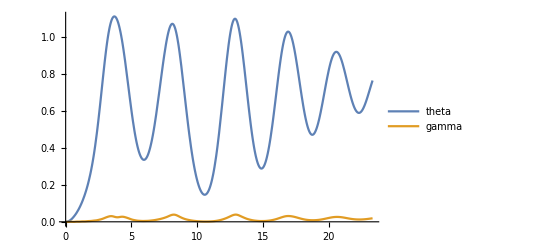

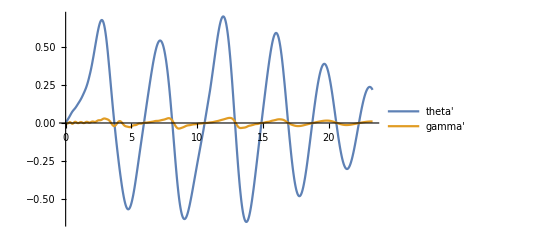

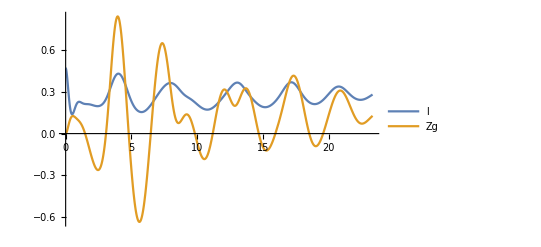

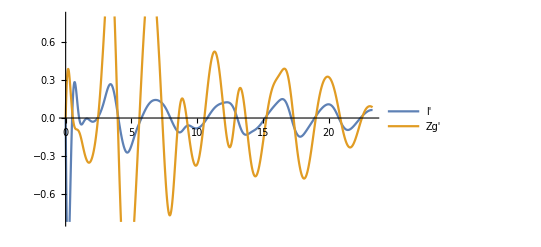

```mathematica
Plot[{th[t]/.s,ga[t]/.s},{t,start,stop},PlotLegends->{"theta","gamma"}]
Plot[{th'[t]/.s,ga'[t]/.s},{t,start,stop},PlotLegends->{"theta'","gamma'"}]
Plot[{l[t]/.s,zg[t]/.s},{t,start,stop},PlotLegends->{"l","Zg"}]
Plot[{l'[t]/.s,zg'[t]/.s},{t,start,stop},PlotLegends->{"l'","Zg'"}]
(*Plot[Fj[t]/.s,{t,0,stop},PlotLegends->{"F浮"}]*)
```

```mathematica
stop
```

-Graphics-

-Graphics-

```mathematica
targets={10,20,40,60,100};
data=Table[{t,First[zg[t]/.s],First[zg'[t]/.s],First[ga[t]/.s],First[ga'[t]/.s]},{t,targets}];
Grid[data,Frame->All]
Export["~/cumcm/cumcm-code/P3-paper.xlsx",data]
```

10 | -0.0664534 | -0.363564 | 0.00334286 | -0.00609852
20 | 0.136743 | 0.322317 | 0.020897 | 0.0150175
40 | -0.0579963 | 0.256131 | 0.00603618 | 0.00134654
60 | 0.287777 | -0.0204315 | 0.025978 | 0.01213
100 | 0.305204 | 0.107308 | 0.0228937 | 0.0187666

~/cumcm/cumcm-code/P3-paper.xlsx

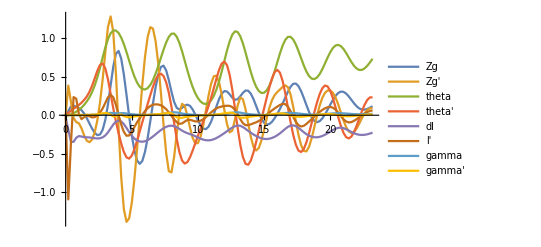

~/cumcm/cumcm-code/P3.xlsx

```mathematica
dl[t_]:=l[t]-l0
data=Table[{t,First[ff[t]/.s]},{ff,{zg,zg',th,th',dl,l',ga,ga'}},{t,0,40/w,0.2}];
save=Table[{t,First[zg[t]/.s],First[zg'[t]/.s],First[th[t]/.s],First[th'[t]/.s],First[dl[t]/.s],First[l'[t]/.s],First[ga[t]/.s],First[ga'[t]/.s]},{t,0,40/w,0.2}];
ListLinePlot[data,PlotLegends->{Zg,Zg',theta,theta',dl,l',gamma,gamma'}]
Export["~/cumcm/cumcm-code/P3.xlsx",save]
```

## 第4题

```mathematica
Clear["Global`*"];
(*AG长度*)
d=1.40792;
(*弹簧原长度*)
l0=0.5;
(*振子质量*)
m=2433;
(*弹簧劲度系数*)
k=80000;
(*小g*)
g=9.8;
(*弹簧旋转刚度*)
krot=250000;
(*浮子质量*)
M=4866;
(*垂荡兴波阻尼系数*)
c0=528.5018;
(*纵摇附加转动惯量*)
I0=7142.493;
(*纵摇激励力矩振幅*)
L=2140;
(*入射波浪频率*)
w=1.9806;
(*垂荡激励力振幅*)
f=1760;
(*浮子转动惯量*)
Ia=8399.2;

(*垂荡附加质量*)
m0=1091.099;
(*纵摇兴波阻尼力矩系数*)
cr0=1655.909;
(*纵摇静水恢复力矩系数*)
Mrec=8890.7;
(*海水密度*)
rho=1025;

(*垂荡静水恢复力(浮力)*)
Fj[t_]:=(5.2609+1.86007*Sec[th[t]]-Pi*zg[t]*Sec[th[t]])*rho*g;
(*激励力*)
Fwave[t_]:=f*Cos[w*t];
(*振子转动惯量*)
(*Ib[t_]:=258.149+774.448l[t]+1548.9l[t]^2;*)
(*Ib[t_]:=MomentOfInertia[Cylinder[{{0,0,0},{0.5,0,0}},0.5],{l[t]+0.5,0,0},{0,0,1}]*)
Ib[t_]:=m/12*(4*0.5^2-12*0.5*(0.5+l[t])+3*1^2+12*(0.5+l[t])^2)
(*纵摇激励力矩*)
Mwave[t_]:=L*Cos[w*t];
(*theta2=theta1+gamma*)
th2[t_]:=th[t]+ga[t];
(*P点x座标*)
xp[t_]:=d*Sin[th[t]]-l[t]*Sin[th2[t]];
(*P点z座标*)
zp[t_]:=zg[t]-d*Cos[th[t]]+l[t]*Cos[th2[t]];
(*PTO系统的力*)
Fpto[t_,c_]:=-k*(l[t]-l0)-c*l'[t];
(*PTO系统的力矩*)
Mpto[t_,crot_]:=-krot*ga[t]-crot*ga'[t];

start=300;
stop=start+10;
dim=1;
```

```mathematica
P4[c_,crot_]:=Sum[(c*(l'[t]^2)+crot*(ga'[t]^2))*dim,{t,start,stop,dim}]/.NDSolve[{m*xp''[t]==-Fpto[t,c]*Sin[th2[t]]+Fab[t]*Cos[th2[t]],m*zp''[t]==Fpto[t,c]*Cos[th2[t]]-m*g+Fab[t]*Sin[th2[t]],Ib[t]*th2''[t]==Mpto[t,crot]+Fab[t]*l[t],M*zg''[t]==Fwave[t]+Fj[t]-M*g-Fpto[t,c]*Cos[th2[t]]-Fab[t]*Sin[th2[t]]-m0*zg''[t]-c0*zg'[t],Ia*th''[t]==Mwave[t]-Mpto[t,crot]+Fab[t]*d*Cos[th[t]]*Cos[th2[t]]-Fab[t]*d*Sin[th[t]]*Sin[th2[t]]-I0*th''[t]-cr0*th'[t]-Mrec*th[t],th'[0]==th[0]==ga[0]==ga'[0]==l'[0]==zg'[0]==0,l[0]==l0-m/k,zg[0]==0},{th,ga,zg,l},{t,start,stop}]
```

```mathematica
CalcP4[kStart_,kStop_,kStepNum_,eStart_,eStop_,eStepNum_]:=Parallelize[Table[{pe,ppk,First[P4[ppk,pe]]},{ppk,Range[kStart,kStop,(kStop-kStart)/kStepNum]},{pe,Range[eStart,eStop,(eStop-eStart)/eStepNum]}]]
```

```mathematica
s=CalcP4[0,100000,8,0,100000,8];
```

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

General::stop: Further output of NDSolve::pdord will be suppressed during this calculation.

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

General::stop: Further output of NDSolve::pdord will be suppressed during this calculation.

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

General::stop: Further output of NDSolve::pdord will be suppressed during this calculation.

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

General::stop: Further output of NDSolve::pdord will be suppressed during this calculation.

-Graphics3D-

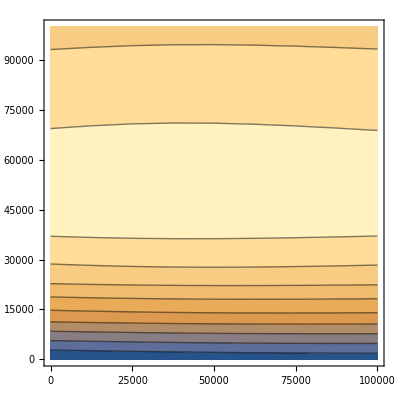

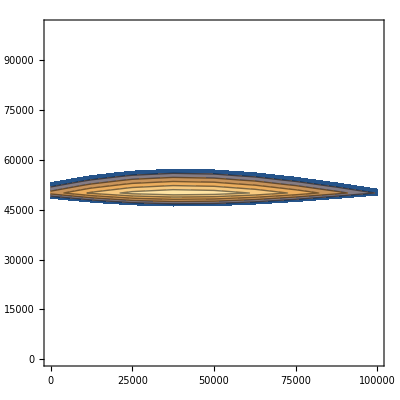

-Graphics3D-

-Graphics-

-Graphics-

```mathematica
(*Grid[N[s],Frame->All]*)
ss=Flatten[s,1];
ListPlot3D[ss]
ListContourPlot[ss]
ListContourPlot[ss,PlotRange->{940,960}]
```